## BSF History

Finds the genome id of the BSF. Warning it searches only the last generation!

```mathematica
findBSFId[genomes_]:=Sort[Flatten[genomes,1],#1⟦4⟧>#2⟦4⟧&]⟦1,1⟧
```

```mathematica
traceBackIds[parentId_Integer,genomes_]:=
Module[{p,n,i,l={}},
n=parentId;
For[i=Length[genomes],i≥1,i--,
p=Cases[genomes⟦i⟧,{n,_,_,_}];
If[p=!={},p=Sequence@@p;PrependTo[l,{i}~Join~p];n=p⟦2⟧;,Null];
];
l
]
```

```mathematica
removeDuplicit[ids_]:=
Module[{i,l={},it},
it=ids⟦1⟧;
For[i=2,i<=Length[ids],i++,
(*Print[all[[i,2]]," ",all⟦i-1,2⟧];*)
If[ids⟦i,4⟧=!=ids⟦i-1,4⟧,
AppendTo[l,it];it=ids⟦i⟧, 
Null
]
];
AppendTo[l,it];
l
]
```

```mathematica
removeDuplicitStructural[ids_]:=
Module[{i,l={},it,bsf},
it=ids⟦1⟧;
For[i=2,i<=Length[ids],i++,
(*Print[all[[i,2]]," ",all⟦i-1,2⟧];*)
If[(ids⟦i,4⟧/._?NumberQ->C)=!=(ids⟦i-1,4⟧/._?NumberQ->C),
AppendTo[l,it];it=ids⟦i⟧, 
Null
];
If[ids⟦i,4⟧=!=ids⟦i-1,4⟧,
bsf=ids⟦i⟧, 
Null
]
];
AppendTo[l,it];
If[bsf≠it,AppendTo[l,bsf]];
l
]
```

```mathematica
onlyNBiggestChanges[ids_,N_]:=ids⟦Sort[Ordering[Abs[#⟦1⟧-#⟦2⟧]&/@Partition[ids⟦All,5⟧,2,1],-N]]⟧
```

```mathematica
listBSFEvolution[fileName_]:=
Module[{genomes},
genomes=ToExpression@StringSplit[Import[fileName],"\n"];
(*onlyNBiggestChanges[traceBackIds[findBSFId[genomes],genomes],15]*)
(*removeDuplicit[traceBackIds[findBSFId[genomes],genomes]]*)
removeDuplicitStructural[traceBackIds[findBSFId[genomes],genomes]]
(*traceBackIds[findBSFId[genomes],genomes]*)
]
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT1D_G2/run_001_045_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 10 | -1 | {plus} | 0.889202
2 | 141 | 10 | {atan[x0]} | 0.374024
3 | 291 | 141 | {atan[1]} | 0.708003
4 | 366 | 291 | {gauss[1]} | 0.904305
5 | 463 | 366 | {gauss[x0,x0]} | 0.88065
6 | 539 | 463 | {gauss[x0,x0,1]} | 0.85151
7 | 686 | 539 | {gauss[x0,x0,1,x0]} | 0.869407
8 | 790 | 686 | {gauss[x0,x0,x0,x0]} | 0.889191
10 | 971 | 875 | {gauss[gauss[x0,x0,x0,x0]]} | 0.58629
11 | 1100 | 971 | {gauss[gauss[x0,1,x0,x0]]} | 0.597504
12 | 1186 | 1100 | {gauss[gauss[x0,1,x0,x0],1]} | 0.909797
48 | 4772 | 4674 | {atan[gauss[gauss[x0,1,x0,x0],1]]} | 0.913181
81 | 8085 | 7962 | {atan[gauss[plus[0.253422 x0,4.63012,-3.30173 x0,3.56862 x0],1]]} | 0.920984
82 | 8171 | 8085 | {atan[gauss[plus[0.313438 x0,4.63012,-3.4533 x0,1.67104 x0],x0]]} | 0.956632)

```mathematica
(evo2=listBSFEvolution["~/java/exp/GPAT1D_G2_3/run_001_080_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 16 | -1 | {plus} | 0.889202
3 | 282 | 116 | {plus[1.]} | 0.58628
4 | 368 | 282 | {plus[0.903801 plus[1.]]} | 0.639866
9 | 884 | 784 | {plus[-1.26582 plus[0.903801 plus[0.980875]]]} | 0.350388
10 | 997 | 884 | {plus[-1.26798 plus[0.903801 plus[0.980875]],0.902662]} | 0.789644
11 | 1083 | 997 | {plus[-0.135731 plus[0.907651 times[1],0.431028],0.902662]} | 0.74496
36 | 3542 | 3426 | {times[plus[-0.4978 plus[0.905331 times[1],0.46595],0.900702]]} | 0.92524
294 | 29333 | 29233 | {times[plus[-0.504142 plus[0.911217 times[1],2.2867],0.900702 times[1]]]} | 0.518428
295 | 29495 | 29333 | {times[plus[-0.502882 times[times[1],1],0.883768 times[1]]]} | 0.90081
305 | 30484 | 30399 | {times[plus[-0.517318 times[times[1],1],0.870291 times[1]],x0]} | 0.182495
306 | 30599 | 30484 | {times[plus[-0.517318 times[times[1],1],0.870291 times[1]],1]} | 0.908
315 | 31481 | 31383 | {times[times[plus[-0.517318 times[times[1],1],0.866519 times[1]],1]]} | 0.908882
322 | 32177 | 32090 | {plus[1. times[plus[-0.556842 times[times[1],1],0.852543 times[1]],1]]} | 0.91898
336 | 33579 | 33478 | {plus[-0.960029 times[plus[-0.585244 times[times[1],1],0.852543 times[1],1.],1]]} | 0.321077
341 | 34084 | 33981 | {plus[-0.477693 times[plus[-0.652563 times[plus[1.91296],1],-1.27212 times[1],1.02472],1]]} | 0.748625
351 | 35062 | 34966 | {plus[-0.371155 times[plus[-0.542426 times[plus[2.31238,1. x0],1],-1.27212 times[1],1.28035],1]]} | 0.39938
352 | 35196 | 35062 | {plus[-0.371155 plus[0.927634 plus[-0.542426 times[plus[2.3149,1. x0],1],-2.46226 times[1],1.28035],2.5465]]} | 0.427218
359 | 35871 | 35766 | {plus[0.00677013 plus[0.93039 plus[-0.542636 times[plus[3.5125,0.880367 x0],1,x0],-2.48147 times[1],2.57033],2.5465]]} | 0.801301
361 | 36094 | 35994 | {plus[-8.72902-4 plus[0.941885 plus[-4.47409 times[plus[-0.363961,0.87894 x0],1,x0],-2.48147 times[1],2.57033],2.16043,1.01357 x0]]} | 0.917695
363 | 36297 | 36193 | {plus[-8.72902-4 plus[-3.26937 plus[1.68752 times[plus[-0.363961,-0.114295 x0],1,x0,x0],-4.74151 times[1],2.57033],4.00817,1.01876 x0]]} | 0.856573
366 | 36587 | 36487 | {plus[-8.72902-4 plus[1.53648 plus[1.68752 times[plus[-0.439413,-0.114295 x0],x0,x0,x0],-4.7867 times[1],4.48212],1.66858,1.01876 x0]]} | 0.989156
370 | 36965 | 36859 | {plus[-8.72902-4 plus[1.53648 plus[1.68752 times[plus[-0.230727,-0.114295 x0],x0,x0,x0],-4.7867 times[1],4.48212],1.74645,0.88784 x0]]} | 0.998223)

```mathematica
rules={times[x__]:>Times[x],plus[x__]:>Plus[x],atan[x__]:>ArcTan[Plus[x]],gauss[x__]:>Exp[-(Plus[x])^2],sin[x__]:>Sin[Plus[x]]};
```

```mathematica
nullRules={times->0,plus->0,atan->0,gauss->0,sin->0};
```

```mathematica
e=Simplify[evo2[[15,4,1]]//.rules/.nullRules]
```

0.714496

```mathematica
eq=Last[evo2][[4,1]]/.rules
```

-8.72902-4 plus[1.53648 plus[1.68752 times[plus[-0.230727,-0.114295 x0],x0,x0,x0],-4.7867 times[1],4.48212],1.74645,0.88784 x0]

```mathematica
eq2=eq/.rules
```

-8.72902-4 (1.74645+0.88784 x0+1.53648 plus[1.68752 times[plus[-0.230727,-0.114295 x0],x0,x0,x0],-4.7867 times[1],4.48212])

```mathematica
eq2//FullForm
```

Plus[-8.72902,Times[-4,Plus[1.74645,Times[0.88784,x0],Times[1.53648,plus[Times[1.68752,times[plus[-0.230727,Times[-0.114295,x0]],x0,x0,x0]],Times[-4.7867,times[1]],4.48212]]]]]

```mathematica
eq3=eq2/.rules
```

-8.72902-4 (1.74645+0.88784 x0+1.53648 (4.48212-4.7867 times[1]+1.68752 times[plus[-0.230727,-0.114295 x0],x0,x0,x0]))

```mathematica
eq3//FullForm
```

ArcTan[Power[E,Times[-1,Power[Plus[4.63012,Times[-0.468817,x0]],2]]]]

```mathematica
eq4=eq3/.rules
```

-8.72902-4 (1.74645+0.88784 x0+1.53648 (-0.304586+1.68752 x0^3 plus[-0.230727,-0.114295 x0]))

```mathematica
eq4/.plus->0
```

ArcTan[ⅇ^(-(0.56648 x0-3.37343 ArcTan[2 x0])^2)]

```mathematica
eq/.plus->0.//FullForm
```

ArcTan[Power[E,Times[-1,Power[Plus[Times[0.56648,x0],Times[-3.37343,atan[0.,x0,x0]]],2]]]]

```mathematica
target=1.5*x0^4+2.3*x0^3-1.1*x0^2+3.7*x0-4.5
```

-4.5+3.7 x0-1.1 x0^2+2.3 x0^3+1.5 x0^4

```mathematica
(target=Simplify[target/(target/.x0->10)])//CForm
```

-0.000261286108288576 + 0.00021483524459282914*x0 - 0.0000638699375816519*Power(x0,2) + 0.00013354623312527216*Power(x0,3) + 0.00008709536942952533*Power(x0,4)

```mathematica
fitness[target_,evolved_]:=
(1/(1+Mean[Table[(target-evolved)^2,{x0,-10,10,20/19}]]))
```

```mathematica
Manipulate[{fitness[target,evo2[[i]][[4,1]]//.rules/.nullRules],Plot[{target,evo2[[i]][[4,1]]//.rules/.nullRules},{x0,-10,10},PlotStyle->Thick]},{i,1,Length[evo2],1}]
```

```mathematica
fitness[target,0.35]
```

0.908697

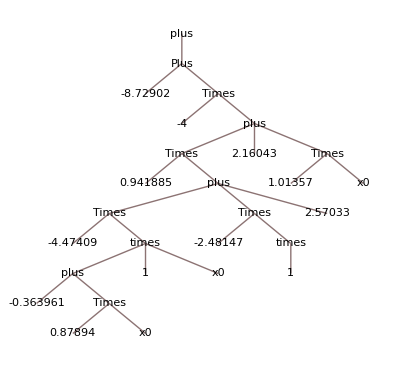

```mathematica
plus[-8.729022744468734-4 plus[0.9418846533694863 plus[-4.474087359196953 times[plus[-0.3639610549683088,0.8789398382106913 x0],1,x0],-2.481471122368675 times[1],2.570325559183874],2.1604341075678932,1.013574957940862 x0]]//TreeForm
```

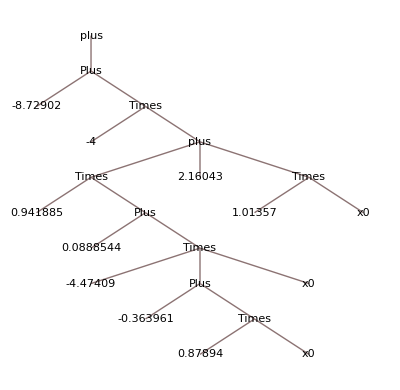

```mathematica
plus[-8.729022744468734-4 plus[0.9418846533694863 (-4.474087359196953 ((-0.3639610549683088+0.8789398382106913 x0)*x0)-2.481471122368675 +2.570325559183874),2.1604341075678932,1.013574957940862 x0]]//TreeForm
```

```mathematica
Grid[{Simplify[(#//.rules/.nullRules)],fitness[target,#//.rules/.nullRules]}&/@evo2[[All,4,1]]]
```

0 | 0.889202
1. | 0.58628
0.903801 | 0.639866
-1.12217 | 0.350388
-0.221424 | 0.789644
0.720961 | 0.74496
0.218079 | 0.92524
-0.711501 | 0.518428
0.380886 | 0.90081
0.352973 x0 | 0.182495
0.352973 | 0.908
0.349201 | 0.908882
0.295701 | 0.91898
-1.21664 | 0.321077
0.714496 | 0.748625
0.462484+0.201324 x0 | 0.39938
-0.105899+0.186755 x0 | 0.427218
0.0177998-0.0120057 x0-0.00300908 x0^2 | 0.801301
-17.7055-10.1893 x0+14.8157 x0^2 | 1.92738×10^-6
-53.1554-4.07505 x0-8.0321 x0^2-2.52233 x0^3 | 6.86166×10^-7
-13.5314-4.07505 x0+4.55731 x0^3+1.18539 x0^4 | 3.755×10^-8
-13.8429-3.55136 x0+2.39296 x0^3+1.18539 x0^4 | 4.20065×10^-8